```mathematica
(*How to calculate Differentiation Matrix Using Lagendre Polynomial*)
```

```mathematica
pp=LegendreP[{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16},τ]
```

{τ,1/2 (-1+3 τ^2),1/2 (-3 τ+5 τ^3),1/8 (3-30 τ^2+35 τ^4),1/8 (15 τ-70 τ^3+63 τ^5),1/16 (-5+105 τ^2-315 τ^4+231 τ^6),1/16 (-35 τ+315 τ^3-693 τ^5+429 τ^7),1/128 (35-1260 τ^2+6930 τ^4-12012 τ^6+6435 τ^8),1/128 (315 τ-4620 τ^3+18018 τ^5-25740 τ^7+12155 τ^9),1/256 (-63+3465 τ^2-30030 τ^4+90090 τ^6-109395 τ^8+46189 τ^10),1/256 (-693 τ+15015 τ^3-90090 τ^5+218790 τ^7-230945 τ^9+88179 τ^11),(231-18018 τ^2+225225 τ^4-1021020 τ^6+2078505 τ^8-1939938 τ^10+676039 τ^12)/1024,(3003 τ-90090 τ^3+765765 τ^5-2771340 τ^7+4849845 τ^9-4056234 τ^11+1300075 τ^13)/1024,(-429+45045 τ^2-765765 τ^4+4849845 τ^6-14549535 τ^8+22309287 τ^10-16900975 τ^12+5014575 τ^14)/2048,(-6435 τ+255255 τ^3-2909907 τ^5+14549535 τ^7-37182145 τ^9+50702925 τ^11-35102025 τ^13+9694845 τ^15)/2048,(6435-875160 τ^2+19399380 τ^4-162954792 τ^6+669278610 τ^8-1487285800 τ^10+1825305300 τ^12-1163381400 τ^14+300540195 τ^16)/32768}

```mathematica
pp[[1]]
```

τ

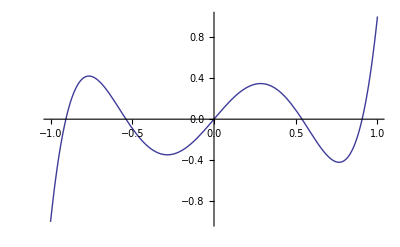

```mathematica
Plot[LegendreP[5,x],{x,-1,1}]
```

```mathematica
dp4=D[pp[[5]],τ]
```

1/8 (15-210 τ^2+315 τ^4)

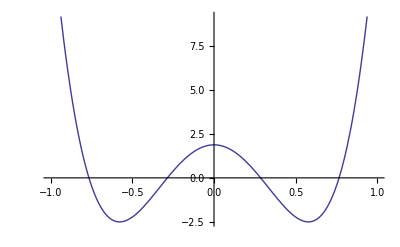

```mathematica
Plot[dp4,{τ,-1,1}]
```

```mathematica
tt1={FindRoot[dp4==0,{τ,0.2}],FindRoot[dp4==0,{τ,0.9}]}
```

{{τ→0.285232},{τ→0.765055}}

```mathematica
tt2={FindRoot[dp4==0,{τ,-0.2}],FindRoot[dp4==0,{τ,-0.9}]}
```

{{τ→-0.285232},{τ→-0.765055}}

```mathematica
nn=5;
```

```mathematica
τ1={-1,-0.7650553239294671,-0.2852315164806451,0.2852315164806451,0.7650553239294671,1};
```

```mathematica
{-nn(nn+1)/4,nn(nn+1)/4}
```

{-15/2,15/2}

```mathematica
pp[[5]]
```

1/8 (15 τ-70 τ^3+63 τ^5)

```mathematica
i=1;k=0;
{τ1[[i+1]],τ1[[k+1]]}
D10= (pp[[5]]/.(τ->  τ1[[k+1]]))/(pp[[5]]/.(τ-> τ1[[i+1]]))/(τ1[[k+1]]-τ1[[i+1]])
```

{-0.765055,-1}

10.1414

```mathematica
For[k=0,k<(nn+1),k++,
For[i=0,i<(nn+1),i++,
Which[
i==k==0,DiffD[i,k]=-nn(nn+1)/4,
i==k==nn,DiffD[i,k]=nn(nn+1)/4,
i==k,DiffD[i,k]=0.0,
i≠k,DiffD[i,k]=(pp[[nn]]/.(τ->  τ1[[k+1]]))/(pp[[nn]]/.(τ-> τ1[[i+1]]))/(τ1[[k+1]]-τ1[[i+1]])]
]]
Table[DiffD[i,k],{k,0,nn},{i,0,nn}]//MatrixForm

(*----------------------------------------------------------------------------------------------------------*)
```

(-15/2 | 10.1414 | -4.03619 | 2.24468 | -1.34991 | 1/2
-1.78636 | 0. | 2.52343 | -1.15283 | 0.653548 | -0.237781
0.484951 | -1.72126 | 0. | 1.75296 | -0.786357 | 0.269701
-0.269701 | 0.786357 | -1.75296 | 0. | 1.72126 | -0.484951
0.237781 | -0.653548 | 1.15283 | -2.52343 | 0. | 1.78636
-1/2 | 1.34991 | -2.24468 | 4.03619 | -10.1414 | 15/2)

```mathematica
dp16=D[pp[[16]],τ]
```

(-1750320 τ+77597520 τ^3-977728752 τ^5+5354228880 τ^7-14872858000 τ^9+21903663600 τ^11-16287339600 τ^13+4808643120 τ^15)/32768

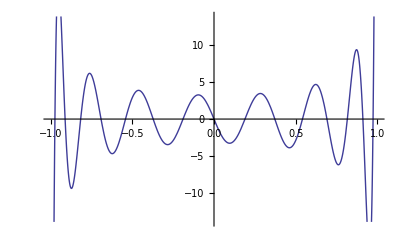

```mathematica
Plot[dp16,{τ,-1,1}]
```

```mathematica
(*15 LGL points of derivative of legendre polynomial of order N=16*)
```

```mathematica
{FindRoot[dp16==0,{τ,0.0}],FindRoot[dp16==0,{τ,0.2}],FindRoot[dp16==0,{τ,0.4}],FindRoot[dp16==0,{τ,0.55}],FindRoot[dp16==0,{τ,0.7}],FindRoot[dp16==0,{τ,0.8}],FindRoot[dp16==0,{τ,0.9}],FindRoot[dp16==0,{τ,0.98}]}
```

{{τ→0.},{τ→0.189512},{τ→0.372174},{τ→0.541385},{τ→0.691029},{τ→0.815696},{τ→0.91088},{τ→0.973132}}

```mathematica
{FindRoot[dp16==0,{τ,-0.2}],FindRoot[dp16==0,{τ,-0.4}],FindRoot[dp16==0,{τ,-0.55}],FindRoot[dp16==0,{τ,-0.7}],FindRoot[dp16==0,{τ,-0.8}],FindRoot[dp16==0,{τ,-0.9}],FindRoot[dp16==0,{τ,0.98}]}
```

{{τ→-0.189512},{τ→-0.372174},{τ→-0.541385},{τ→-0.691029},{τ→-0.815696},{τ→-0.91088},{τ→0.973132}}